# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Solutions 04

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1

You are given the following annual data on four investments, i∈{1,2,3,4} in a market M:

r_f=0.02

μ_M=0.085

σ_M=0.105

β={0.9,1.2,0.6,2.1}

σ_ϵ={0.05,0.07,0.04,0.09}

Under the assumption that the CAPM applies:

Compute the mean vector of the asset returns.

Compute the correlation and covariance matrices of the asset returns.

Compute the mean-variance efficient portfolio such that 𝟙^T x=1. Assume there are no further constraints, specifically, that short positions are permitted

Compute the mean and standard deviation of that portfolio.

The investor wishes to keep 10% of its assets in cash and place the remainder in the optimal portfolio. Assuming returns are Normally distributed what are the mean and standard deviation of return for this combined cash-risky portfolio?

### Solution

```mathematica
nRiskFree=0.02;
nMktMean=0.085;
nMktSdev=0.105;
vnBeta={0.9,1.2,0.6,2.1};
vnErrSdev={0.05,0.07,0.04,0.09};
```

We can use the CAPM to compute the mean vector and covariance matrix, and then use these statistics to compute the correlation matrix.

μ_i=r_f+β_i(μ_M-r_f)

```mathematica
vnMean=nRiskFree+vnBeta(nMktMean-nRiskFree);
mnCovariance=nMktSdev KroneckerProduct[vnBeta,vnBeta]+DiagonalMatrix[vnErrSdev^2];
```

The correlation matrix first requires us to extract the standard deviations from the covariance matrix and then use them to normalize the covariances using ρ_(i,j)=σ_(i,j)/σ_i σ_j.

```mathematica
vnSdev=√Diagonal[mnCovariance];
mnCorrelation=mnCovariance/KroneckerProduct[vnSdev,vnSdev];
```

The Print[ ] function is useful for simple reporting.

```mathematica
Print["μ = ",MatrixForm[vnMean]]
Print["Σ = ",MatrixForm[mnCovariance]]
Print["C = ",MatrixForm[mnCorrelation]]
```

μ = (0.0785
0.098
0.059
0.1565)

Σ = (0.08755 | 0.1134 | 0.0567 | 0.19845
0.1134 | 0.1561 | 0.0756 | 0.2646
0.0567 | 0.0756 | 0.0394 | 0.1323
0.19845 | 0.2646 | 0.1323 | 0.47115)

C = (1. | 0.970026 | 0.965399 | 0.97711
0.970026 | 1. | 0.963989 | 0.975683
0.965399 | 0.963989 | 1. | 0.971029
0.97711 | 0.975683 | 0.971029 | 1.)

The efficient mean-variance solution is x_i∝β_i/σ_ϵ_i and portfolio mean and standard deviation are

```mathematica
vnX=#/Total[#]&[vnBeta/vnErrSdev^2];
Print["x = ",MatrixForm[vnX]]
```

x = (0.29052
0.197633
0.302625
0.209222)

```mathematica
nPortMean=vnMean.vnX;
nPortSdev=√(vnX.mnCovariance.vnX);
Print["μ_𝒫 = " ,nPortMean]
Print["σ_𝒫 = ",nPortSdev]
```

μ_𝒫 = 0.092772

σ_𝒫 = 0.364025

Given a 10% cash position, ϕ=0.9 below

((σ_(𝒫(ϕ)))/(μ_(𝒫(ϕ))))=(1-ϕ) (0/r_f) + ϕ (σ_𝒫/μ_𝒫)

```mathematica
ϕ=0.9;
{nLeverageSdev,nLeverageMean}=(1-ϕ){0,nRiskFree}+ϕ{nPortSdev,nPortMean};
```

```mathematica
Print[MatrixForm[{"σ_(𝒫 (0.9))","μ_(𝒫 (0.9))"}]," = ",MatrixForm[{nLeverageSdev,nLeverageMean}]]
```

(σ_(𝒫 (0.9))
μ_(𝒫 (0.9))) = (0.327622
0.0854948)

## Question 2

You have a portfolio with estimated monthly mean return of 0.8% and monthly standard deviation of 3.5%.

Assuming the portfolio returns follow a Normal distribution, what is the VaR and CVaR at a 99.9% confidence level?

Assuming the portfolio returns follow a Student t distribution with 4 degrees of freedom, what is the VaR and CVaR at a 99.9% confidence level?

Note: Consider a random variable R\[Distributed]StudentTDistribution[μ,σ,ν]. Generally, the parameter μ is known as a location parameter and σ a scale parameter. The mean of the Student t is μ, but it standard deviation is not σ, but

StandardDeviation[R]=σ √(ν/(ν-2))

Thus, the parameter σ is related to but not identical to the standard deviation. Given the standard deviation as in this problem, you must solve for the Student t scale parameter σ to specify the distribution correctly.

```mathematica
StandardDeviation[StudentTDistribution[m,s,d]]
```

Piecewise[{{√(d/(-2+d)) s, d>2}, {Indeterminate, True}}]

### Solution

The scale parameter σ of the Student t distribution with ν degrees of freedom can be calculated by

scale=√((ν-2)/ν)sdev

The VaR and CVaR are calculated

VaR_(δ, χ)=argmin_r[1-F_δ(r) ≤ 1-χ]

CVaR_(δ, χ)=E[ r | r ≤ VaR_(δ,χ)] =1/(1-χ)∫_(-∞)^(VaR_(δ, χ)) r ⅆF_δ[r]

#### Normal

The required parameters for the Normal distribution are

```mathematica
nPortMu=0.008;
nPortSigma=0.035;
nConfLevel=0.999;
```

The VaR and CVaR are

```mathematica
nVaRN=InverseCDF[NormalDistribution[nPortMu,nPortSigma],1-nConfLevel]
```

-0.100158

```mathematica
nCVaRN=1/(1-nConfLevel)Integrate[r PDF[NormalDistribution[nPortMu,nPortSigma],r],{r,-∞,nVaRN}]
```

-0.109848

#### Student t

We need the degrees of freedom and scale.

```mathematica
nDegOfFree=4;
nTScale=√((nDegOfFree-2)/nDegOfFree)nPortSigma;
```

And the VaR and CVaR are

```mathematica
nVaRT=InverseCDF[StudentTDistribution[nPortMu,nTScale,nDegOfFree],1-nConfLevel]
```

-0.169527

```mathematica
nCVaRT=1/(1-nConfLevel)Integrate[r PDF[StudentTDistribution[nPortMu,nTScale,nDegOfFree],r],{r,-∞,nVaRT}]
```

-0.231722

#### Summary

We can produce a nice report by using the Grid[ ] function. The argument is a 2×1 column vector consisting of a title string and a TableForm[ ] object. Note the use of Style[ ] to format the title text.

```mathematica
?Grid
```

Note that subscripts can be entered as, for example, "nVaRNCtrl_0.999”. If there is following text, then hitting the right-arrow-key (not the character →) will bring you back up a level to the baseline. Superscripts work the same way using “xCtrl^2” and a right-arrow will bring you down to the text baseline. You don’t have to hit the shift-key, so it’s actually “nVaRNCtrl-0.999” for nVaR_0.999 and “xCtrl62” for x^2.

```mathematica
Grid[
{
{Style["Results",FontSize->18]},{TableForm[{{nVaRN,nVaRT},{nCVaRN,nCVaRT}},TableHeadings->{{"VaR_0.999","CVaR_0.999"},{"Normal","StudentT(Cell["ν=4",ExpressionUUID->"39976529-9a7e-4df3-adfe-b3e590316e43"])"}}]}
},
Frame->All
]
```

Results
 | Normal | StudentT(Cell["ν=4"])
VaR_0.999 | -0.100158 | -0.169527
CVaR_0.999 | -0.109848 | -0.231722

The risk measures for a Normal versus Student t with ν=4 are quite different, even though the distributions appear somewhat similar. Also observe that, compared with the Normal, the Student t shows a higher concentration close about the mean but is punctuated by occasional large excursions to the tails.

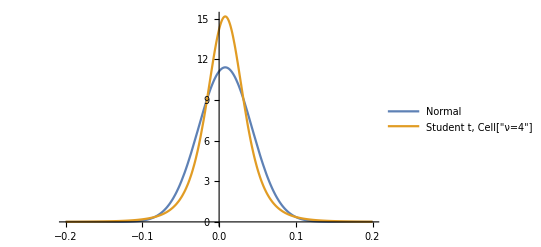

```mathematica
Plot[{PDF[NormalDistribution[nPortMu,nPortSigma],r],PDF[StudentTDistribution[nPortMu,nTScale,nDegOfFree],r]},{r,-0.2,0.2},PlotLegends->{"Normal", "Student t, Cell["ν=4",ExpressionUUID->"801f61db-a6bb-4ed5-9dfa-e28ffd3654ee"]"},PlotRange->All]
```

Note the tail.

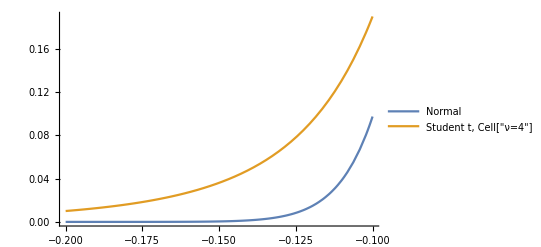

```mathematica
Plot[{PDF[NormalDistribution[nPortMu,nPortSigma],r],PDF[StudentTDistribution[nPortMu,nTScale,nDegOfFree],r]},{r,-0.2,-0.1},PlotLegends->{"Normal", "Student t, Cell["ν=4",ExpressionUUID->"0e0aa3b9-a02b-4b62-b29f-754d0e89c665"]"},PlotRange->All]
```